```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"tooth_naive.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

targets=<|2->{0.2,0.8},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
epsilon=0.01;
stepsize=0.05;
```

{0.1,0.3,0.6}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
(*(* prototype first-order and second-order methods *)
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
previous={{0,0,0},{0,0,0}};
list=Table[Module[{peaks,mean,steps,rms,f1,f0,diff,square,derivative,xx,dx,yy,df,factor},
mean=visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
derivative=2*(mean-target);
square=(mean-target)^2;
If[Norm[First@previous]>0,{f1,f0,xx,yy}=previous,{f1,f0,xx,yy}={derivative,square,peaks,mean}];
(*diff=mean-y1;
steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,(target-mean)*(peaks-x1)/(mean-y1)*stepsize,2*(target-mean)*stepsize];*)
(*dx=peaks-xx;
df=If[Product[dx[[i]],{i,Length[dx]}]≠0,(mean-yy)/dx,1];*)
(*derivative=derivative*df;*)
diff=derivative-f1;
previous={derivative,square,peaks,mean};
df=If[Product[diff[[i]],{i,Length[diff]}]≠0,-(square-f0)/diff*stepsize,-derivative*stepsize];(*should be second-order but look like first-order*)
dx=-derivative*stepsize;
steps=Table[If[Abs[dx[[i]]]>Abs[df[[i]]],dx[[i]],df[[i]]],{i,Length[mean]}];
(*steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,-derivative*(peaks-xx)/diff*stepsize,-derivative*stepsize];*)
(*steps=-derivative*stepsize;*)
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
{mean,peaks,rms,steps,dx,df,Table[Abs[df[[i]]]>Abs[dx[[i]]],{i,Length[dx]}]}
],{30}];*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,negativegradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
negativegradient:=-2*(mean-target)*stepsize;
(*steps=If[First@previous==0,negativegradient,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=rms-Table[RootMeanSquare[Table[If[i==n,mean0[[i]],mean[[i]]],{i,Length[mean]}]-target],{n,Length[mean]}];
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,dy/dx,negativegradient]
]];*)
steps=If[First@previous==0,negativegradient,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=mean-mean0;
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,negativegradient*dy/dx,negativegradient]
]];
previous={rms,mean,peaks};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,55}];
```

-3.6536582896275229×10^9

0

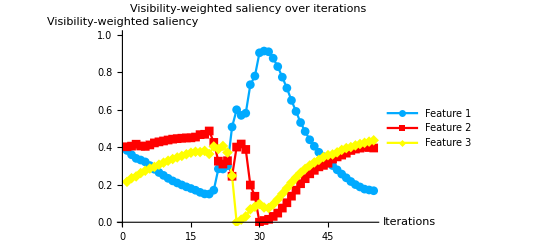

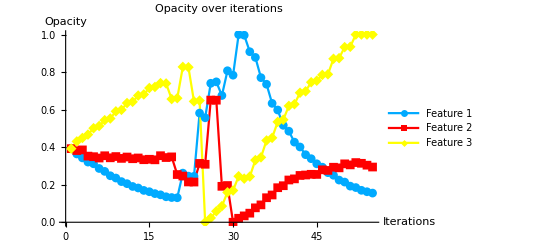

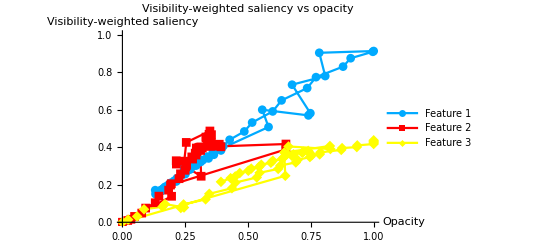

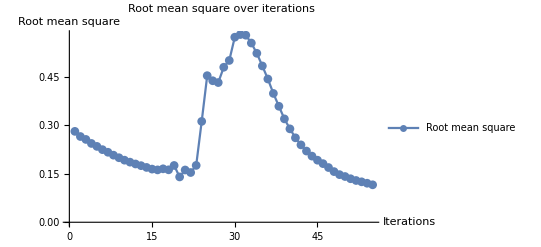

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps
1 | 0.382547
0.40209
0.215363 | 0.392157
0.392157
0.392157 | 0.281781 | -0.0282547
-0.010209
0.0384637
2 | 0.359689
0.405531
0.234781 | 0.363902
0.381948
0.430621 | 0.265807 | -0.0210092
0.00355627
0.0184379
3 | 0.340198
0.415733
0.24407 | 0.342893
0.385504
0.449058 | 0.256759 | -0.0222836
-0.0331999
0.0179315
4 | 0.33158
0.4063
0.26212 | 0.320609
0.352304
0.46699 | 0.24433 | -0.00895623
-0.00302021
0.034013
5 | 0.321407
0.40423
0.274364 | 0.311653
0.349284
0.501003 | 0.235176 | -0.0251492
-0.00714427
0.0117217
6 | 0.302088
0.411956
0.285956 | 0.286504
0.34214
0.512725 | 0.22509 | -0.0155237
0.0121077
0.0310583
7 | 0.2823
0.422674
0.295027 | 0.27098
0.354247
0.543783 | 0.217018 | -0.0232378
-0.0108591
0.00890661
8 | 0.265119
0.428253
0.306628 | 0.247742
0.343388
0.552689 | 0.207991 | -0.0122077
0.00658921
0.0382128
9 | 0.249629
0.433069
0.317302 | 0.235535
0.349977
0.590902 | 0.200012 | -0.0189863
-0.00972596
0.0078967
10 | 0.234008
0.438166
0.327826 | 0.216549
0.340252
0.598799 | 0.192464 | -0.0110255
0.00724109
0.0362719
11 | 0.220435
0.442759
0.336806 | 0.205523
0.347493
0.635071 | 0.186329 | -0.0148267
-0.00905509
0.00651641
12 | 0.209416
0.445247
0.345337 | 0.190696
0.338438
0.641587 | 0.180667 | -0.00813143
0.00399107
0.0333377
13 | 0.198759
0.447757
0.353484 | 0.182565
0.342429
0.674925 | 0.175457 | -0.0129433
-0.00929308
0.0060242
14 | 0.188585
0.449249
0.362166 | 0.169622
0.333136
0.680949 | 0.169988 | -0.00696302
0.00239592
0.0342761
15 | 0.1798
0.449717
0.370482 | 0.162659
0.335531
0.715225 | 0.164785 | -0.0100682
-0.00292706
0.00556895
16 | 0.170589
0.453882
0.375529 | 0.15259
0.332604
0.720794 | 0.162327 | -0.00645816
0.0218945
0.020342
17 | 0.159334
0.466643
0.374023 | 0.146132
0.354499
0.741136 | 0.165687 | -0.0103404
-0.00971255
-0.0016731
18 | 0.150999
0.46864
0.380361 | 0.135792
0.344786
0.739463 | 0.162564 | -0.00411115
0.00346783
-0.0832089
19 | 0.150075
0.486167
0.363758 | 0.131681
0.348254
0.656254 | 0.176045 | -0.00112541
-0.0940907
0.00471377
20 | 0.170889
0.425317
0.403795 | 0.130555
0.254163
0.660968 | 0.140506 | 0.131106
-0.00810449
0.166647
21 | 0.284487
0.325469
0.390044 | 0.261661
0.246059
0.827615 | 0.162034 | -0.0159852
-0.0313777
-0.00173241
22 | 0.283603
0.310075
0.406323 | 0.245676
0.214681
0.825883 | 0.154189 | -0.00101571
-0.000494274
-0.181984
23 | 0.300656
0.32775
0.371594 | 0.24466
0.214187
0.643899 | 0.176259 | 0.336893
0.0992325
0.00435871
24 | 0.507427
0.245103
0.24747 | 0.581553
0.31342
0.648257 | 0.31267 | -0.0250062
-0.00457219
-1.00391
25 | 0.599427
0.400573
0. | 0.556547
0.308847
0. | 0.454438 | 0.183744
0.341982
0.0229048
26 | 0.569326
0.416742
0.0139319 | 0.740291
0.650829
0.0229048 | 0.438699 | 0.00768851
-0.000551963
0.0356477
27 | 0.580962
0.387945
0.0310932 | 0.74798
0.650277
0.0585525 | 0.433095 | -0.0727879
-0.458826
0.027388
28 | 0.732799
0.198218
0.0689824 | 0.675192
0.191451
0.0859405 | 0.480546 | 0.132004
0.00420872
0.0734621
29 | 0.778927
0.138424
0.082649 | 0.807195
0.19566
0.159403 | 0.501565 | -0.0237247
-0.229556
0.00962465
30 | 0.902792
0.
0.0972083 | 0.783471
0.
0.169027 | 0.573665 | 0.419131
0.0212241
0.0760576
31 | 0.912116
0.00927045
0.0786139 | 1.
0.0212241
0.245085 | 0.581922 | -0.00349705
0.0126987
-0.0127467
32 | 0.908306
0.0157552
0.0759388 | 0.996503
0.0339229
0.232338 | 0.579883 | -0.0880575
0.0145153
0.010998
33 | 0.873873
0.031076
0.0950508 | 0.908445
0.0484382
0.243336 | 0.55563 | -0.0302605
0.0283847
0.0877487
34 | 0.829141
0.0488313
0.122028 | 0.878185
0.0768228
0.331085 | 0.523829 | -0.107785
0.0157112
0.0146945
35 | 0.772963
0.0754928
0.151544 | 0.7704
0.092534
0.345779 | 0.48456 | -0.0350752
0.0380983
0.0900798
36 | 0.714805
0.103866
0.181329 | 0.735325
0.130632
0.435859 | 0.444124 | -0.101941
0.0146068
0.0138434
37 | 0.6493
0.139061
0.21164 | 0.633385
0.145239
0.449702 | 0.399356 | -0.0352971
0.038778
0.0850332
38 | 0.590475
0.17104
0.238486 | 0.598088
0.184017
0.534736 | 0.359578 | -0.0817411
0.010635
0.0114134
39 | 0.531212
0.205258
0.26353 | 0.516347
0.194652
0.546149 | 0.320485 | -0.0312631
0.0304834
0.073831
40 | 0.483705
0.232059
0.284236 | 0.485083
0.225136
0.61998 | 0.28957 | -0.0583072
0.00597332
0.00885569
41 | 0.43947
0.258084
0.302446 | 0.426776
0.231109
0.628836 | 0.261747 | -0.025754
0.0182623
0.0611865
42 | 0.404795
0.276639
0.318566 | 0.401022
0.249371
0.690022 | 0.239896 | -0.0410374
0.00237358
0.00741437
43 | 0.372759
0.295186
0.332055 | 0.359985
0.251745
0.697437 | 0.220768 | -0.0212932
0.00376144
0.0487485
44 | 0.349517
0.30316
0.347323 | 0.338692
0.255506
0.746185 | 0.205032 | -0.0272343
-0.000669772
0.00791368
45 | 0.328061
0.3145
0.357439 | 0.311457
0.254836
0.754099 | 0.192404 | -0.0179675
0.0245506
0.0310061
46 | 0.302043
0.336584
0.361373 | 0.29349
0.279387
0.785105 | 0.181753 | -0.0292573
-0.00329077
0.00302801
47 | 0.279415
0.348199
0.372386 | 0.264232
0.276096
0.788133 | 0.169628 | -0.0138763
0.0170129
0.0827824
48 | 0.256724
0.357864
0.385412 | 0.250356
0.293109
0.870915 | 0.157013 | -0.0256277
-0.00328729
0.00337651
49 | 0.236784
0.368149
0.395067 | 0.224728
0.289822
0.874292 | 0.147594 | -0.0106427
0.0213205
0.0586035
50 | 0.217085
0.382439
0.400476 | 0.214086
0.311142
0.932895 | 0.141792 | -0.0216722
-0.00552583
0.00184142
51 | 0.20066
0.39
0.40934 | 0.192414
0.305617
0.934737 | 0.134887 | -0.00762872
0.0123136
0.0917816
52 | 0.188038
0.395024
0.416938 | 0.184785
0.31793
1. | 0.129476 | -0.014566
-0.00387689
0.00213121
53 | 0.176552
0.400178
0.42327 | 0.170219
0.314053
1. | 0.125339 | -0.00765518
-0.0100178
0.017673
54 | 0.171912
0.398474
0.429614 | 0.162564
0.304035
1. | 0.120968 | -0.00719117
-0.0098474
0.0170386
55 | 0.167909
0.39551
0.436582 | 0.155373
0.294188
1. | 0.116102 | -0.00679087
-0.00955098
0.0163418

```mathematica
t2-t1
iteration
saliency4=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_difference.png",saliency4];
opacity4=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_difference.png",opacity4];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity4=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_difference.png",saliencyopacity4];
rms4=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_difference.png",rms4];
table4=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_difference.png",table4];
(*path1=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path4=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path4]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,40}];
```

-3.6536583209148266×10^9

0

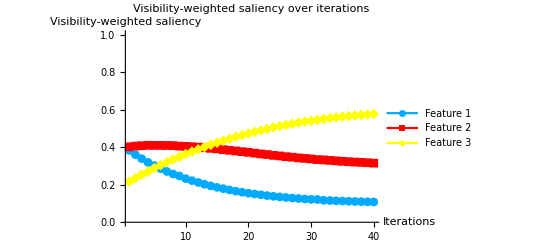

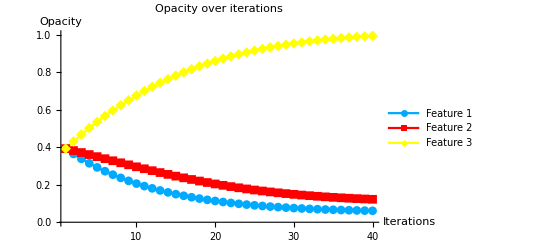

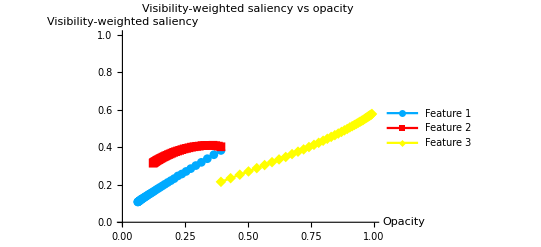

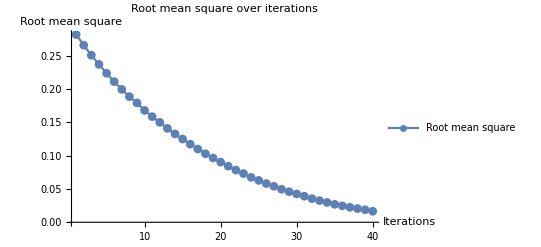

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps
1 | 0.382547
0.40209
0.215363 | 0.392157
0.392157
0.392157 | 0.281781 | -0.0282547
-0.010209
0.0384637
2 | 0.359689
0.405531
0.234781 | 0.363902
0.381948
0.430621 | 0.265807 | -0.0259689
-0.0105531
0.0365219
3 | 0.338536
0.407997
0.253467 | 0.337933
0.371395
0.467143 | 0.250764 | -0.0238536
-0.0107997
0.0346533
4 | 0.31915
0.410134
0.270717 | 0.31408
0.360595
0.501796 | 0.237054 | -0.021915
-0.0110134
0.0329283
5 | 0.302061
0.409669
0.28827 | 0.292165
0.349582
0.534724 | 0.223631 | -0.0202061
-0.0109669
0.031173
6 | 0.285728
0.40962
0.304652 | 0.271959
0.338615
0.565897 | 0.211142 | -0.0185728
-0.010962
0.0295348
7 | 0.270681
0.409113
0.320205 | 0.253386
0.327653
0.595432 | 0.199435 | -0.0170681
-0.0109113
0.0279795
8 | 0.257035
0.408176
0.334789 | 0.236318
0.316741
0.623412 | 0.18859 | -0.0157035
-0.0108176
0.0265211
9 | 0.246713
0.40554
0.347747 | 0.220614
0.305924
0.649933 | 0.17916 | -0.0146713
-0.010554
0.0252253
10 | 0.232366
0.404468
0.363166 | 0.205943
0.29537
0.675158 | 0.167854 | -0.0132366
-0.0104468
0.0236834
11 | 0.221682
0.402242
0.376077 | 0.192706
0.284923
0.698841 | 0.158536 | -0.0121682
-0.0102242
0.0223923
12 | 0.211942
0.399984
0.388074 | 0.180538
0.274699
0.721234 | 0.149934 | -0.0111942
-0.00999842
0.0211926
13 | 0.202516
0.396746
0.400738 | 0.169344
0.2647
0.742426 | 0.140919 | -0.0102516
-0.00967458
0.0199262
14 | 0.193904
0.393644
0.412452 | 0.159092
0.255026
0.762352 | 0.132616 | -0.0093904
-0.00936438
0.0187548
15 | 0.185944
0.390754
0.423302 | 0.149702
0.245661
0.781107 | 0.12496 | -0.00859443
-0.00907537
0.0176698
16 | 0.178895
0.386826
0.434279 | 0.141108
0.236586
0.798777 | 0.117227 | -0.00788948
-0.00868264
0.0165721
17 | 0.172185
0.383107
0.444709 | 0.133218
0.227903
0.815349 | 0.109898 | -0.00721849
-0.00831065
0.0155291
18 | 0.165538
0.379657
0.454805 | 0.126
0.219593
0.830878 | 0.10283 | -0.00655381
-0.00796572
0.0145195
19 | 0.160104
0.375993
0.463903 | 0.119446
0.211627
0.845398 | 0.0964537 | -0.00601037
-0.00759935
0.0136097
20 | 0.154798
0.37251
0.472691 | 0.113435
0.204028
0.859008 | 0.0903108 | -0.00547983
-0.00725104
0.0127309
21 | 0.150596
0.368131
0.481273 | 0.107956
0.196777
0.871738 | 0.0842571 | -0.00505962
-0.00681306
0.0118727
22 | 0.14635
0.364045
0.489605 | 0.102896
0.189964
0.883611 | 0.0783948 | -0.00463499
-0.00640453
0.0110395
23 | 0.142139
0.360694
0.497167 | 0.0982609
0.183559
0.894651 | 0.0731074 | -0.00421393
-0.00606936
0.0102833
24 | 0.138192
0.356506
0.505302 | 0.094047
0.17749
0.904934 | 0.0673777 | -0.00381916
-0.00565063
0.00946979
25 | 0.134963
0.353245
0.511792 | 0.0902278
0.171839
0.914404 | 0.0628175 | -0.00349625
-0.00532454
0.0088208
26 | 0.132243
0.349354
0.518403 | 0.0867316
0.166515
0.923224 | 0.0581192 | -0.00322434
-0.00493537
0.00815971
27 | 0.129057
0.346607
0.524336 | 0.0835072
0.161579
0.931384 | 0.0539805 | -0.00290571
-0.00466074
0.00756645
28 | 0.126492
0.342991
0.530517 | 0.0806015
0.156918
0.938951 | 0.0495915 | -0.00264924
-0.00429908
0.00694832
29 | 0.124
0.340202
0.535798 | 0.0779523
0.152619
0.945899 | 0.0458771 | -0.00240001
-0.00402021
0.00642022
30 | 0.122061
0.337347
0.540592 | 0.0755523
0.148599
0.952319 | 0.0424688 | -0.00220609
-0.00373471
0.0059408
31 | 0.121357
0.333552
0.545091 | 0.0733462
0.144864
0.95826 | 0.0391444 | -0.00213565
-0.00335524
0.0054909
32 | 0.117219
0.332165
0.550616 | 0.0712105
0.141509
0.963751 | 0.0354488 | -0.00172191
-0.00321649
0.0049384
33 | 0.115786
0.329474
0.55474 | 0.0694886
0.138293
0.968689 | 0.0324878 | -0.00157863
-0.00294736
0.004526
34 | 0.114283
0.327129
0.558588 | 0.06791
0.135345
0.973215 | 0.0297485 | -0.00142833
-0.00271286
0.00414119
35 | 0.112997
0.324442
0.56256 | 0.0664817
0.132632
0.977356 | 0.0268829 | -0.00129973
-0.00244422
0.00374395
36 | 0.111843
0.322384
0.565773 | 0.0651819
0.130188
0.9811 | 0.024582 | -0.00118433
-0.00223841
0.00342274
37 | 0.110663
0.320557
0.56878 | 0.0639976
0.12795
0.984523 | 0.0224424 | -0.00106633
-0.00205568
0.00312202
38 | 0.109727
0.318815
0.571458 | 0.0629313
0.125894
0.987645 | 0.0205202 | -0.000972665
-0.0018815
0.00285417
39 | 0.108948
0.317103
0.573949 | 0.0619586
0.124013
0.990499 | 0.0187191 | -0.000894817
-0.00171026
0.00260508
40 | 0.108079
0.314835
0.577086 | 0.0610638
0.122302
0.993104 | 0.0164354 | -0.000807898
-0.00148346
0.00229136

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_fixed.png",saliencyopacity1];
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_fixed.png",table1];
(*path1=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

4.9395478

4

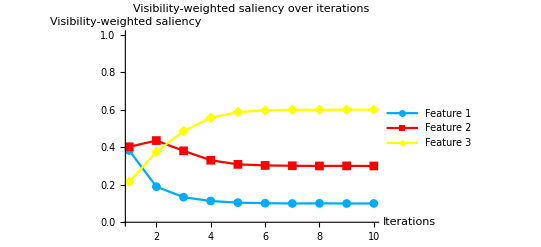

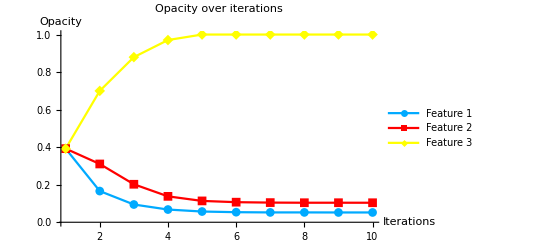

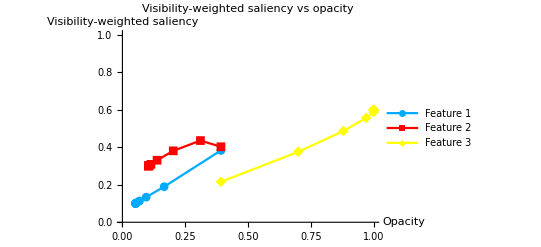

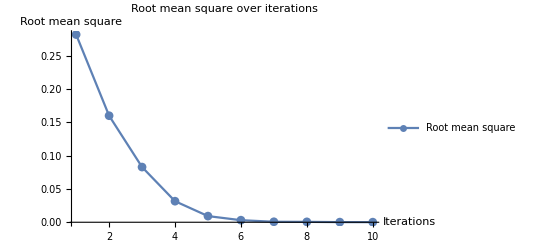

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.382547
0.40209
0.215363 | 0.392157
0.392157
0.392157 | 0.281781 | -0.0282547
-0.010209
0.0384637 | 8
2 | 0.1895
0.435153
0.375347 | 0.166119
0.310485
0.699867 | 0.159943 | -0.00894997
-0.0135153
0.0224653 | 8
3 | 0.133508
0.380465
0.486027 | 0.0945195
0.202362
0.879589 | 0.0828398 | -0.00335078
-0.00804653
0.0113973 | 8
4 | 0.113211
0.330386
0.556403 | 0.0677133
0.13799
0.970768 | 0.0316151 | -0.00132106
-0.00303864
0.00435969 | 8
5 | 0.104409
0.308438
0.587154 | 0.0571448
0.113681
1. | 0.00923138 | -0.00044086
-0.000843763
0.00128462 | 8
6 | 0.101547
0.302776
0.595678 | 0.0536179
0.106931
1. | 0.00309718 | -0.000154655
-0.000277566
0.000432221 | 8
7 | 0.0999417
0.3009
0.599158 | 0.0523807
0.10471
1. | 0.000712199 | 5.82855×10^-6
-0.0000899942
0.0000841657 | 8
8 | 0.100769
0.299889
0.599342 | 0.0524273
0.10399
1. | 0.000587935 | -0.0000769091
0.0000110912
0.0000658179 | 4
9 | 0.0999337
0.300275
0.599791 | 0.0521197
0.104034
1. | 0.000202845 | 6.62757×10^-6
-0.0000274849
0.0000208574 | 4
10 | 0.10009
0.299799
0.600111 | 0.0521462
0.103925
1. | 0.000142288 | -8.98564×10^-6
0.0000200854
-0.0000110998 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_parallelsearch.png",saliencyopacity2];
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_parallelsearch.png",table2];
(*path2=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

8.8595303

4

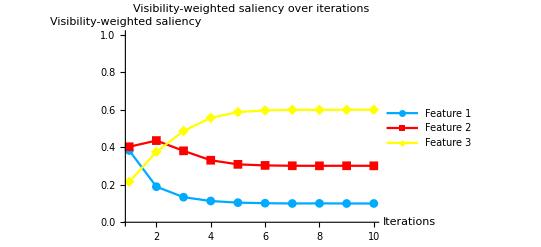

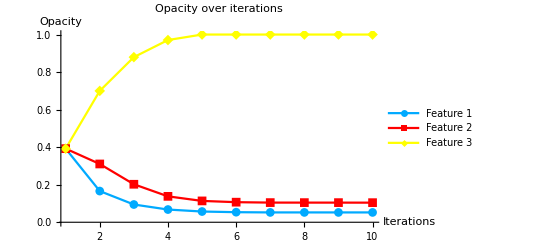

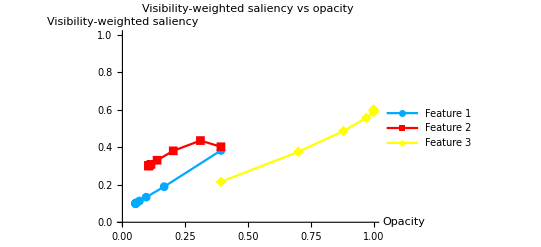

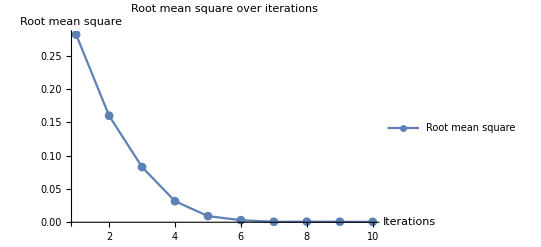

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.382547
0.40209
0.215363 | 0.392157
0.392157
0.392157 | 0.281781 | -0.0282547
-0.010209
0.0384637 | 8
2 | 0.1895
0.435153
0.375347 | 0.166119
0.310485
0.699867 | 0.159943 | -0.00894997
-0.0135153
0.0224653 | 8
3 | 0.133508
0.380465
0.486027 | 0.0945195
0.202362
0.879589 | 0.0828398 | -0.00335078
-0.00804653
0.0113973 | 8
4 | 0.113211
0.330386
0.556403 | 0.0677133
0.13799
0.970768 | 0.0316151 | -0.00132106
-0.00303864
0.00435969 | 8
5 | 0.104409
0.308438
0.587154 | 0.0571448
0.113681
1. | 0.00923138 | -0.00044086
-0.000843763
0.00128462 | 8
6 | 0.101547
0.302776
0.595678 | 0.0536179
0.106931
1. | 0.00309718 | -0.000154655
-0.000277566
0.000432221 | 8
7 | 0.0999417
0.3009
0.599158 | 0.0523807
0.10471
1. | 0.000712199 | 5.82855×10^-6
-0.0000899942
0.0000841657 | 1
8 | 0.100554
0.300612
0.598834 | 0.0523865
0.10462
1. | 0.000824845 | -0.000055358
-0.0000612432
0.000116601 | 1
9 | 0.0998711
0.300925
0.599203 | 0.0523311
0.104559
1. | 0.000708918 | 0.0000128864
-0.0000925474
0.000079661 | 2
10 | 0.100013
0.300662
0.599325 | 0.0523569
0.104374
1. | 0.000545807 | -1.31489×10^-6
-0.0000661803
0.0000674952 | 8

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_linesearch.png",saliencyopacity3];
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_linesearch.png",table3];
(*path3=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

```mathematica
recordxml=NotebookDirectory[]<>"~images\\records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

tooth_naive→{{-3.6536582896275229×10^9,0,{0.155373,0.294188,1.}},{-3.6536583209148266×10^9,0,{0.0610638,0.122302,0.993104}},{4.9395478,4,{0.0521462,0.103925,1.}},{8.8595303,4,{0.0523569,0.104374,1.}}}

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
Clear[f];
Clear[data];
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[NotebookDirectory[]<>dataname<>"_parameterspace.png",sp];
Export[NotebookDirectory[]<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[NotebookDirectory[]<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],NotebookDirectory[]<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],NotebookDirectory[]<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],NotebookDirectory[]<>dataname<>"_optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics-

-Graphics-